```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Sinusoidal CPR McCumber - Stewart paramter =0, + Sinusoidal driving RF (normalized amplitude β and normalized freqeuncy ξ)
```

```mathematica
ysol10=ParametricNDSolveValue[{α+β*Sin[ξ*τ]==Sin[ϕ[τ]]+ϕ'[τ],ϕ[0]==k},ϕ,{τ,0,2000},{α,β,ξ,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol10[α,β,ξ,k][τ],τ,x],β*Sin[ξ*x]}, {x, 0,100 },PlotRange->All],{α,0.0001,2},{β,0,1},{ξ,0.1,2},{k,0,2*Pi}]
```

```mathematica
Manipulate[Plot[ysol[α,β,ξ,k][x], {x, 0,100 },PlotRange->All],{α,0.0001,2},{β,0,1},{ξ,0.1,2},{k,0,2*Pi}]
```

```mathematica
Sinusoidal CPR McCumber - Stewart paramter =g, + Sinusoidal driving RF (normalized amplitude β and normalized freqeuncy ξ)
```

```mathematica
ysol11=ParametricNDSolveValue[{α+β*Sin[ξ*τ]==Sin[ϕ[τ]]+ϕ'[τ]+g*ϕ''[τ],ϕ[0]==k,ϕ'[0]==0},ϕ,{τ,0,2000},{α,β,ξ,g,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ysol11[α,β,ξ,g,0][x]/Pi,2,4,6}, {x, 0,100 },PlotRange->All],{α,0.0001,2},{β,0,1},{ξ,0.1,2},{g,0.000001,6}]
```

```mathematica
Manipulate[Plot[{ND[ysol11[α,β,ξ,g,0][τ],τ,x],β*Sin[ξ*x]}, {x, 0,60 },PlotRange->{{-10,60},All}],{α,0.0001,2},{β,0,1},{ξ,0.1,2},{g,0.000001,6}]
```

```mathematica
Sinusoidal CPR McCumber - Stewart paramter =g, Triangular pulse RF (normalized amplitude β, normalized rise time ξτ and delay d)
```

```mathematica
ysol12=ParametricNDSolveValue[{α+β*HeavisideLambda[ξ(τ-d)]==Sin[ϕ[τ]]+ϕ'[τ]+g*ϕ''[τ],ϕ[0]==k,ϕ'[0]==0},ϕ,{τ,0,2000},{α,β,ξ,g,d,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol12[α,β,ξ,g,d,0][τ],τ,x],β*HeavisideLambda[ξ(x-d)]}, {x, 0,100 },PlotRange->{{-5,80},All}],{α,0.0001,2},{β,0,10},{ξ,0.1,10},{d,10,20},{g,0.000001,6}]
```

```mathematica
Smooth (differentiable) Sawtooth CPR McCumber - Stewart paramter =g, Triangular pulse RF (normalized amplitude β, normalized rise time ξτ and delay d)
```

```mathematica
ysol13=ParametricNDSolveValue[{α+β*HeavisideLambda[ξ(τ-d)]==(swt[((ϕ[τ]/(2*Pi)))-0.5,1,0.005,1.133575])+ϕ'[τ]+g*ϕ''[τ],ϕ[0]==k,ϕ'[0]==0},ϕ,{τ,0,2000},{α,β,ξ,g,d,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol13[α,β,ξ,g,d,0][τ],τ,x],β*HeavisideLambda[ξ(x-d)]}, {x, 0,100 },PlotRange->{{-5,80},All}],{α,0.0001,2},{β,0,10},{ξ,0.001,10},{d,10,20},{g,0.000001,6}]
```

```mathematica
Inductance distorted sinusoidal CPR (Deaver and Pierce), McCumber - Stewart paramter =g, Triangular pulse RF (normalized amplitude β, normalized rise time ξτ and delay d)
```

```mathematica
ysol14=ParametricNDSolveValue[{α+β*HeavisideLambda[ξ(τ-d)]==v[ϕ[τ],l]+ϕ'[τ]+g*ϕ''[τ],ϕ[0]==k,ϕ'[0]==0},ϕ,{τ,0,2000},{α,β,ξ,g,d,l,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol14[α,β,ξ,g,d,l,0][τ],τ,x],β*HeavisideLambda[ξ(x-d)]}, {x, 0,100 },PlotRange->{{-5,80},All}],{α,0.0001,2},{β,0,10},{ξ,0.001,10},{d,10,20},{g,0.000001,6},{l,0,0.2}]
```

```mathematica
Inductance distorted sinusoidal CPR (Deaver and Pierce), McCumber - Stewart paramter =g, Rectangular pulse pulse RF (normalized amplitude β, normalized rise time ξτ and delay d)
```

```mathematica
ysol15=ParametricNDSolveValue[{α+β*UnitStep[τ-d]==v[ϕ[τ],l]+ϕ'[τ]+g*ϕ''[τ],ϕ[0]==k,ϕ'[0]==0},ϕ,{τ,0,2000},{α,β,g,d,l,k}]
```

ParametricFunction[<>]

```mathematica
Manipulate[Plot[{ND[ysol15[α,β,g,d,l,0][τ],τ,x],β*UnitStep[x-d]}, {x, 0,100 },PlotRange->{{-5,80},All}],{α,0.0001,2},{β,0,10},{d,10,20},{g,0.000001,6},{l,0,0.2}]
```

```mathematica
Manipulate[Plot[{β*UnitStep[x-d]}, {x, 0,100 },PlotRange->{{-5,80},All}],{β,0,10},{d,10,20}]
```

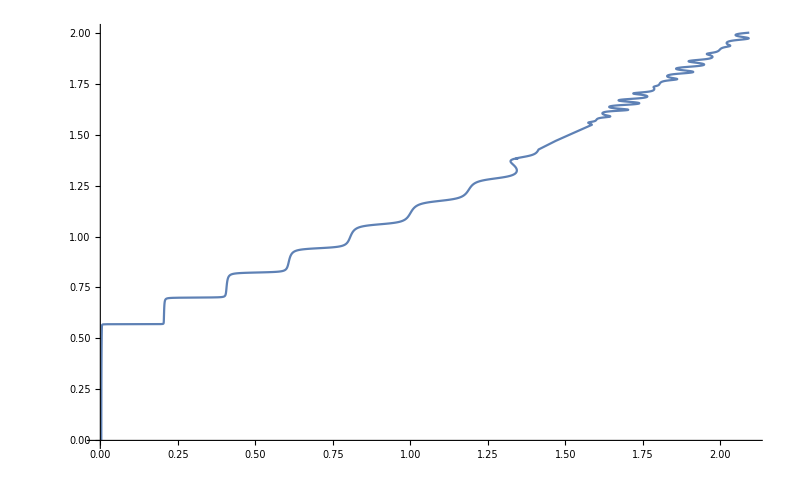

```mathematica
AbsoluteTiming[axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
Plot[NIntegrate[ND[ysol[α, 0.5, 0.1, 0][τ], τ, x], {x, (8*Pi)/0.2, ((12*Pi)/0.2)},MaxRecursion->20]/((4*Pi)/0.2),{α,0.001,2}]//axisFlip]
```

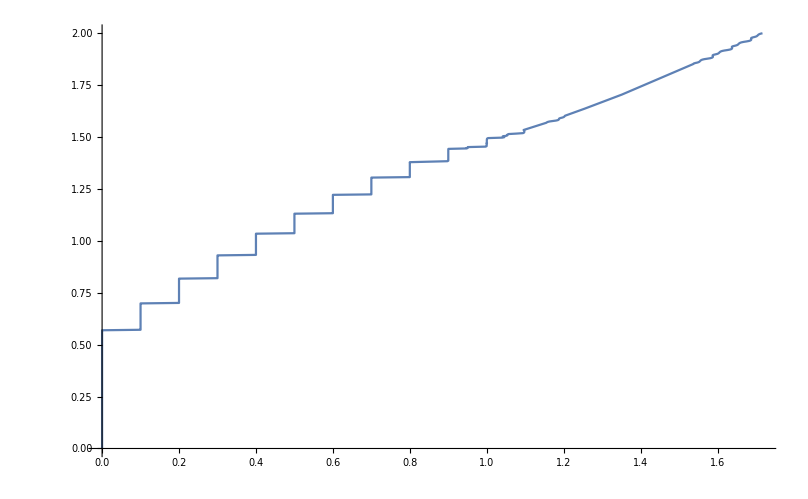

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
List[NIntegrate[ND[ysol[α, 0.5, 0.1, 0][τ], τ, x], {x, (8*Pi)/0.2, ((10*Pi)/0.2)},MaxRecursion->25]/((8*Pi)/0.2),{α,0.001,2},PlotPoints->10]//axisFlip
```

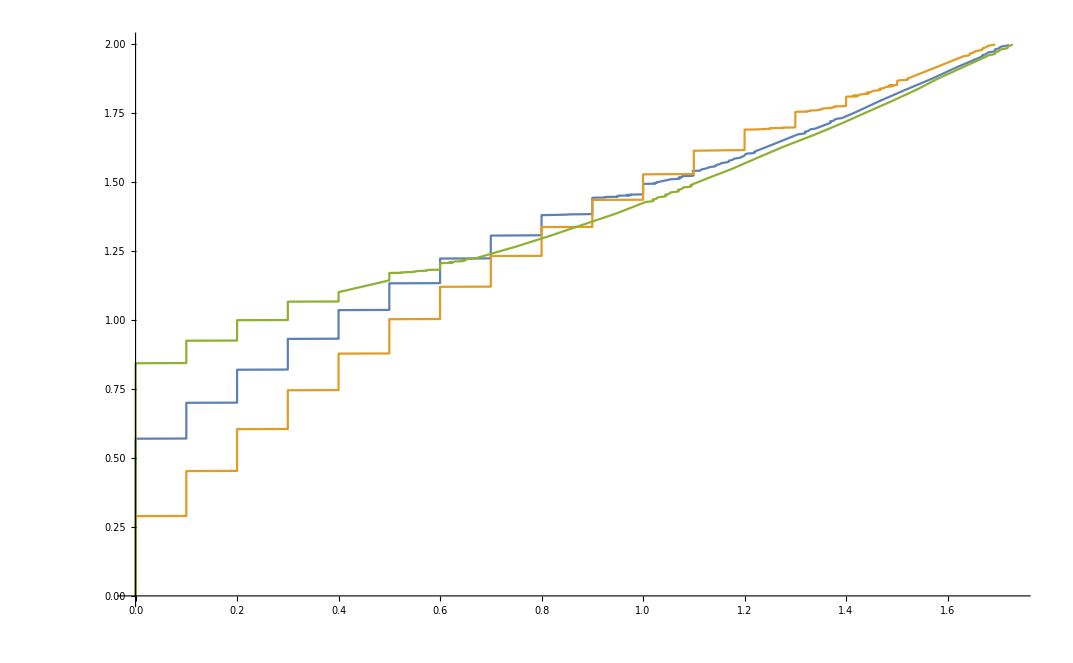

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;
Plot[{NIntegrate[ND[ysol[α, 0.5, 0.1, 0][τ], τ, x], {x, ((8*Pi))/0.1,((16*Pi)/0.1)},MaxRecursion->30,PrecisionGoal->10]/((8*Pi)/0.1),NIntegrate[ND[ysol[α, 0.8, 0.1, 0][τ], τ, x],{x, ((8*Pi))/0.1,((16*Pi)/0.1)},MaxRecursion->30,PrecisionGoal->10]/((8*Pi)/0.1),NIntegrate[ND[ysol[α, 0.2, 0.1, 0][τ], τ, x], {x, ((8*Pi))/0.1,((16*Pi)/0.1)},MaxRecursion->30,PrecisionGoal->10]/((8*Pi)/0.1)},{α,0.001,2}]//axisFlip
```

```mathematica
axisFlip=#/.{x_Line|x_GraphicsComplex:>MapAt[#~Reverse~2&,x,1],x:(PlotRange->_):>x~Reverse~2}&;Plot[{NIntegrate[ND[ysol[α, 0.5, 1, 0][τ], τ, x],{x,((8*Pi))/0.8,((16*Pi)/0.8)},MaxRecursion->30,PrecisionGoal->10]/((8*Pi/0.8)),NIntegrate[ND[ysol[α, 0.8, 1, 0][τ], τ, x],{x,((8*Pi))/0.8,((16*Pi)/0.8)},MaxRecursion->30,PrecisionGoal->10]/((8*Pi/0.8)),NIntegrate[ND[ysol[α, 0.2, 1, 0][τ], τ, x], {x,((8*Pi))/0.8,((16*Pi)/0.8)},MaxRecursion->30,PrecisionGoal->10]/((8*Pi/0.8))},{α,0.001,2}]//axisFlip
```